```mathematica
ClearAll["Global`*"]
R1=48;

res=out/.NDSolve[{out'[t]==t*R1, out[0]==1},out, {t,0,10}, Method->"ExplicitRungeKutta",MaxStepSize->0.1][[1]];
resNumber=res[2]
```

97.

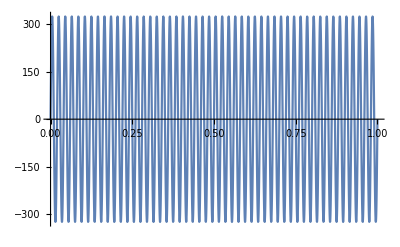

```mathematica
Plot[Sqrt[2]*230*Sin[2*Pi*50*t],{t,0,1}]
```

```mathematica
fce[t_]:=Sqrt[2]*230*Sin[2*Pi*50*t];
fce[5*10^(-3)]
```

230 √2

```mathematica
N[5*10^(-3)]
```

0.005

```mathematica
N[Pi*120/180]
```

2.0944

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
data=Import["./../code/test-program/cmodel/output.csv"];
ctuBlue=RGBColor["#0065BD"];
ctuLightBlue=RGBColor["#6AADE4"];
ctuRed=RGBColor["#C60C30"];
ctuGreen=RGBColor["#A2AD00"];
ctuGreenyBlue=RGBColor["#00B2A9"];
ctuOrange=RGBColor["#E05206"];
ctuYellow=RGBColor["#F0AB00"];
```

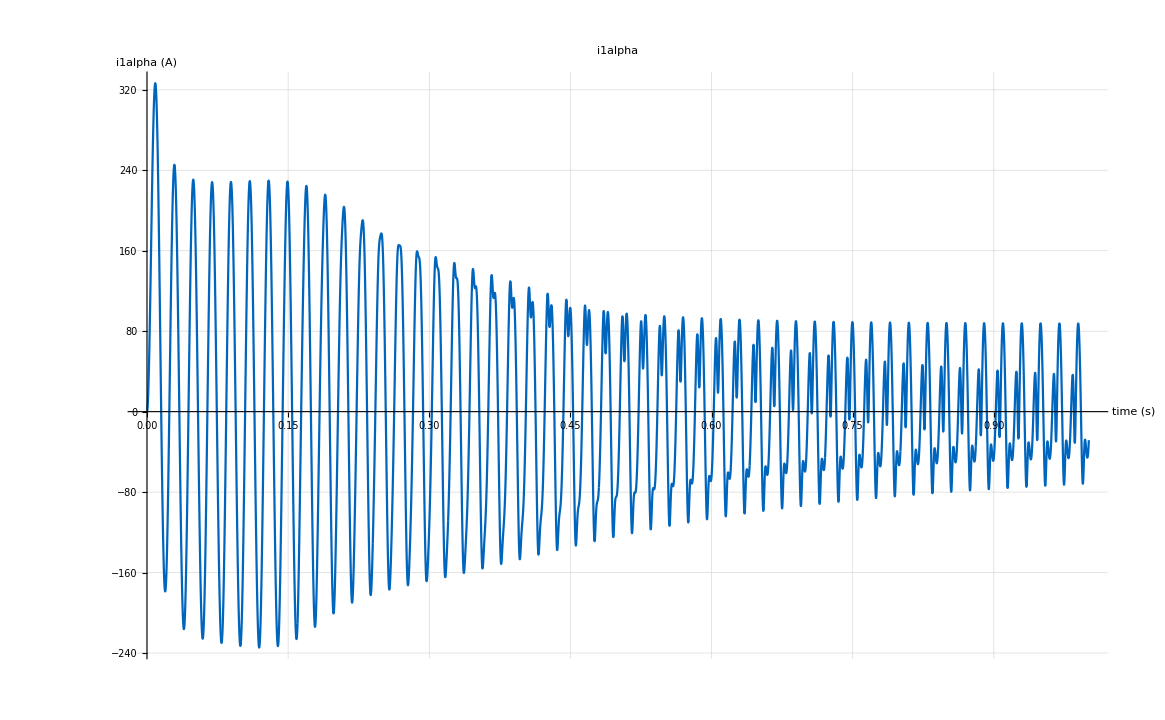

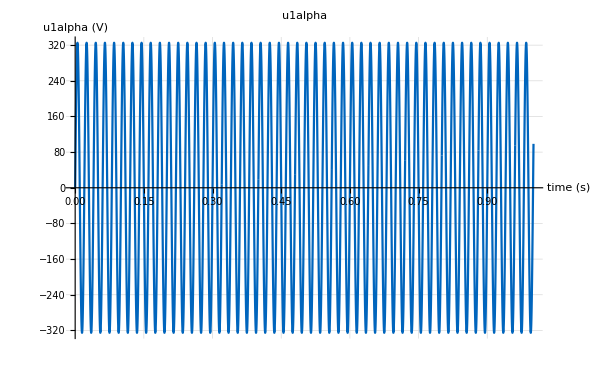

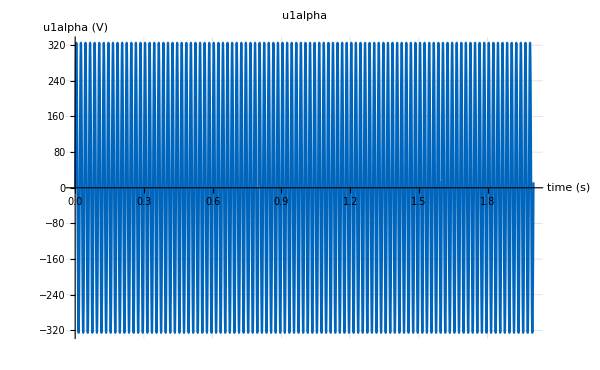

```mathematica
ListPlot[data[[All,1;;2]],Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","i1alpha (A)"},PlotLabel->"i1alpha",PlotRangeClipping->False,ImageSize->600]

ListPlot[data[[All,{1,3}]],Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","u1alpha (V)"},PlotLabel->"u1alpha",PlotRangeClipping->False,ImageSize->600]
```

```mathematica
N[Sqrt[2]*230]
```

325.269